# ASEN 5007-Homework 6

## Zach Dischner & Greg Nelson

## Helpful Modules

```mathematica
PrintWithStyle[x_] := Module[{color=LightGreen},Framed[Style[x,18,Bold,Background->color],
Background->color]
]
```

Cell 7: Simple function to print output for solutions in a stylazed way

```mathematica
PrintWithStyleMat[x_] := Module[{color=LightGreen},Style[x,
Background->color]
]
```

Turner triangle  K matrix calculation

```mathematica
Trig3TurnerMembraneStiffness[ncoor_,Emat_,h_,numer_]:=Module[{x1,x2,x3,y1,y2,y3,x21,x32,x13,y12,y23,y31,A,Be,Ke},{{x1,y1},{x2,y2},{x3,y3}}=ncoor;A=Simplify[(x2*y3-x3*y2+(x3*y1-x1*y3)+(x1*y2-x2*y1))/2];{x21,x32,x13,y12,y23,y31}={x2-x1,x3-x2,x1-x3,y1-y2,y2-y3,y3-y1};Be={{y23,0,y31,0,y12,0},{0,x32,0,x13,0,x21},{x32,y23,x13,y31,x21,y12}}/(2*A);
If[numer,Be=N[Be]];Ke=A*h*Transpose[Be].Emat.Be;
Return[Ke]];
```

Integrate some function over the turner triangle

```mathematica
IntegrateOverTriangle[expr_,tcoord_,A_,max_]:=Module[{p,i,j,k,z1,z2,z3,c,s=0},p=Expand[expr];{z1,z2,z3}=tcoord;
For[i=0,i≤max,i++,For[j=0,j≤max,j++,For[k=0,k≤max,k++,c=Coefficient[Coefficient[Coefficient[p,z1,i],z2,j],z3,k];
s+=2*c*(i!*j!*k!)/((i+j+k+2)!);]]];
Return[Simplify[A*s]]];
```

## Problem 1-Book 15.3

Compute consistant node force vector over a Turner triangle using varying thickness outlined in 15.1

```mathematica
Clear[Fe,heq,bmat,zmat,h,p,h1,h2,h3,by1,by2,by3]
(*Set up Triangle coordinates and modulus matrices*)
coords = {{x1,y1},{x2,y2},{x3,y3}};
Emat = {{E11,E12,E13},{E12,E22,E23},{E13,E23,E33}};
(*Height, as dictated by E15.1 [ h(ζ1,ζ2,ζ3)=h1ζ1+h2ζ2+h3ζ3]*)
heq=h1*ζ1+h2*ζ2+h3*ζ3;
(*b matrix of 'pressures' from the book*)
bmat = {{0},{by1*ζ1+by2*ζ2+ by3*ζ3}};
(*Form the "pressure" function to integrate over the traingle*)
zmat = {{ζ1,0},{0,ζ1},{ζ2,0},{0,ζ2},{ζ3,0},{0,ζ3}};
p = heq*zmat.bmat;
(*Compute the consistant force vector*)
Fe=IntegrateOverTriangle[p,{ζ1,ζ2,ζ3},A,3];
PrintWithStyle["Fe = "]PrintWithStyleMat[Simplify[Fe]//MatrixForm]
h1=h;h2=h;h3=h;by1=by;by2=by;by3=by;
PrintWithStyle["Checking, with uniform 'h' and 'b' values, Fe = "]PrintWithStyle[Fe//MatrixForm]
```

Fe =  (0
1/60 A (2 by1 (3 h1+h2+h3)+by2 (2 h1+2 h2+h3)+by3 (2 h1+h2+2 h3))
0
1/60 A (by1 (2 h1+2 h2+h3)+2 by2 (h1+3 h2+h3)+by3 (h1+2 (h2+h3)))
0
1/60 A (by1 (2 h1+h2+2 h3)+2 by3 (h1+h2+3 h3)+by2 (h1+2 (h2+h3))))

Checking, with uniform 'h' and 'b' values, Fe =  (0
(A by h)/3
0
(A by h)/3
0
(A by h)/3)

## Problem 2-Book 15.4

Derive Formula for consistent force vector over Turner triangle as described in the book exercise. Code is given. 
qx = qx1ζ1 + qx2ζ2 = qx1(1 − ζ2) + qx2ζ2
qy = qy1ζ1 + qy2ζ2 = qy1(1 − ζ2) + qy2ζ2

```mathematica
ClearAll[ux1,uy1,ux2,uy2,ux3,uy3,z2,L12];
ux=ux1*(1-z2)+ux2*z2;uy=uy1*(1-z2)+uy2*z2;
qx=qx1*(1-z2)+qx2*z2;qy=qy1*(1-z2)+qy2*z2;
We=Simplify[L12*Integrate[qx*ux+qy*uy,{z2,0,1}]];
fe=Table[Coefficient[We,{ux1,uy1,ux2,uy2,ux3,uy3}[[i]]],{i,1,6}];
fe=Simplify[fe];Print["fe=",fe//MatrixForm]
PrintWithStyle["First, displacement equations (15.15) were simplified, since for this force, [z3=0] and  [z2=1-z1]. Then E15.3 was integrated along the path from 1-2, where Gammae varies from 0 to 1 in terms of z2 (or 1 to zero in terms of z1). L12 is a constant length, and can be pulled from the integration. The u transposed q term was multiplied out in the integrand."]
```

fe=(1/6 L12 (2 qx1+qx2)
1/6 L12 (2 qy1+qy2)
1/6 L12 (qx1+2 qx2)
1/6 L12 (qy1+2 qy2)
0
0)

First, displacement equations (15.15) were simplified, since for this force, [z3=0] and  [z2=1-z1]. Then E15.3 was integrated along the path from 1-2, where Gammae varies from 0 to 1 in terms of z2 (or 1 to zero in terms of z1). L12 is a constant length, and can be pulled from the integration. The u transposed q term was multiplied out in the integrand.

```mathematica
ClearAll[h]
PrintWithStyle["Now, I perform the calculation myself"]
(*Define Turner shape functionn Nmat*)
Nmat = {{z1,0},{0,z1},{z2,0},{0,z2},{z3,0},{0,z3}};
(*Calcualte t hat, which is the forces divided by the constant thickness*)
that = {{qx},{qy}}/h;
(*Make substitutions. z3=0 for this integral, and z2 = 1-z1. *)
z2=1-z1;
z3 = 0;
(*Perform the integration*)
fe =Integrate[L12*Nmat.that,{z1,0,1}];
PrintWithStyle["Fe = "]PrintWithStyle[Simplify[fe]//MatrixForm]
PrintWithStyle["This matches the given code from above"]
```

Now, I perform the calculation myself

Fe =  ((L12 (2 qx1+qx2))/(6 h)
(L12 (2 qy1+qy2))/(6 h)
(L12 (qx1+2 qx2))/(6 h)
(L12 (qy1+2 qy2))/(6 h)
0
0)

This matches the given code from above

## Problem 3-Book 15.5

Compute the entries of Ke for the following plane stress triangle :

x1 = 0, y1 = 0, x2 = 3, y2 = 1, x3 = 2, y3 = 2,
| 100   25    0  |
E= |  25   100   0  |      
|   0    0    50   |
h=1

Code from 15.5 solves this exercise:

```mathematica
Clear[h]
(*Set up Triangle coordinates and modulus matrices*)
coords = {{0,0},{3,1},{2,2}}
Emat = {{100,25,0},{25,100,0},{0,0,50}}
h = 1
Ke= Simplify[Trig3TurnerMembraneStiffness[coords,Emat,h,True]];
PrintWithStyle["Ke = "]PrintWithStyle[Ke//MatrixForm]
PrintWithStyle["Ke[1,1] and Ke[6,6] are verified! Yay!!!"]
```

{{0,0},{3,1},{2,2}}

{{100,25,0},{25,100,0},{0,0,50}}

1

Ke =  (18.75 | 9.375 | -12.5 | -6.25 | -6.25 | -3.125
9.375 | 18.75 | 6.25 | 12.5 | -15.625 | -31.25
-12.5 | 6.25 | 75. | -37.5 | -62.5 | 31.25
-6.25 | 12.5 | -37.5 | 75. | 43.75 | -87.5
-6.25 | -15.625 | -62.5 | 43.75 | 68.75 | -28.125
-3.125 | -31.25 | 31.25 | -87.5 | -28.125 | 118.75)

Ke[1,1] and Ke[6,6] are verified! Yay!!!

## Problem 4-Book 16.4

A shape function for a single bar element, with natural coordinates in ξ must be of polynomial fit:
		N1(ξ)=a +a ξ+a ξ2	 N2(ξ)=b +b ξ+b ξ2	 N3(ξ)=c +c ξ+c ξ2.
Determina a0 - c2, given the node value conditions described in the following image

-Graphics-

## A-N1:

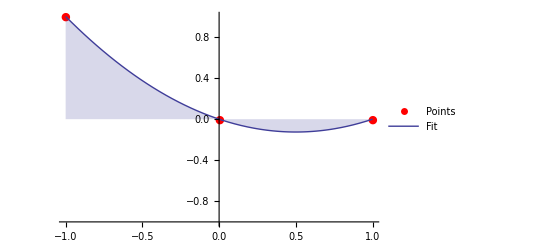

a coefficients are:  {a0→6.40988×10^-17,a1→-0.5,a2→0.5}

```mathematica
ClearAll[ξ]
conditions={{-1,1},{0,0},{1,0}};
a=FindFit[conditions,a0+a1*ξ+a2*ξ^2,{a0,a1,a2},ξ];
N1 = Fit[conditions,{1,ξ,ξ^2},ξ];
Show[ListPlot[conditions,PlotStyle->Red,AxesOrigin->{0,-1},PlotLegends->{"Points"},PlotMarkers->{Automatic,Medium}],Plot[{N1},{ξ,-1,1},Filling->{1->0},PlotLegends->{"Fit"} ]]
PrintWithStyle["a coefficients are: "]PrintWithStyle[a]
```

## B-N2:

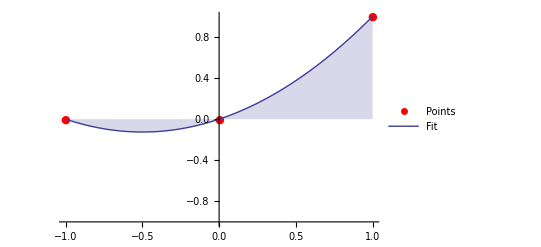

b coefficients are:  {b0→-1.28198×10^-16,b1→0.5,b2→0.5}

```mathematica
ClearAll[ξ]
conditions={{-1,0},{0,0},{1,1}};
b=FindFit[conditions,b0+b1*ξ+b2*ξ^2,{b0,b1,b2},ξ];
N2 = Fit[conditions,{1,ξ,ξ^2},ξ];
Show[ListPlot[conditions,PlotStyle->Red,AxesOrigin->{0,-1},PlotLegends->{"Points"},PlotMarkers->{Automatic,Medium}],Plot[{N2},{ξ,-1,1},Filling->{1->0},PlotLegends->{"Fit"} ]]
PrintWithStyle["b coefficients are: "]PrintWithStyle[b]
```

## C-N3:

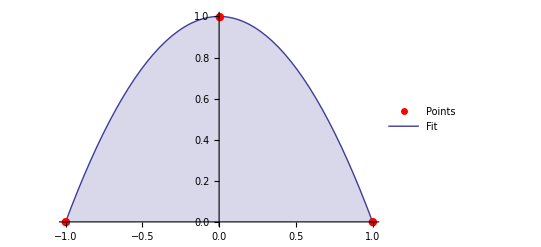

a coefficients are:  {c0→1.,c1→-1.57009×10^-16,c2→-1.}

```mathematica
ClearAll[ξ]
conditions={{-1,0},{0,1},{1,0}};
c=FindFit[conditions,c0+c1*ξ+c2*ξ^2,{c0,c1,c2},ξ];
N3 = Fit[conditions,{1,ξ,ξ^2},ξ];
Show[ListPlot[conditions,PlotStyle->Red,AxesOrigin->{0,0},PlotLegends->{"Points"},PlotMarkers->{Automatic,Medium}],Plot[{N3},{ξ,-1,1},Filling->{1->0},PlotLegends->{"Fit"} ]]
PrintWithStyle["a coefficients are: "]PrintWithStyle[c]
```

Final Check, sum the N equations

```mathematica
sumN =N1+N2+N3;
ξ=10000;
PrintWithStyle["Sum of all shape functions Σ N(ξ) =  "] 
PrintWithStyle[sumN]
```

Sum of all shape functions Σ N(ξ) =

1.